```mathematica
Get["NeutronBeam/ManualShift_NBeamInt.m"]
```

Set::wrsym: Symbol pmax is Protected.

### check integrand

```mathematica
?BinIntShift
```

```mathematica
XAShift=0.00009717735268126651
```

0.0000971774

```mathematica
YAShift=0.007308000000000092;
```

```mathematica
YDetShift=0.008729653897695132;
```

```mathematica
XDetShift=0;
```

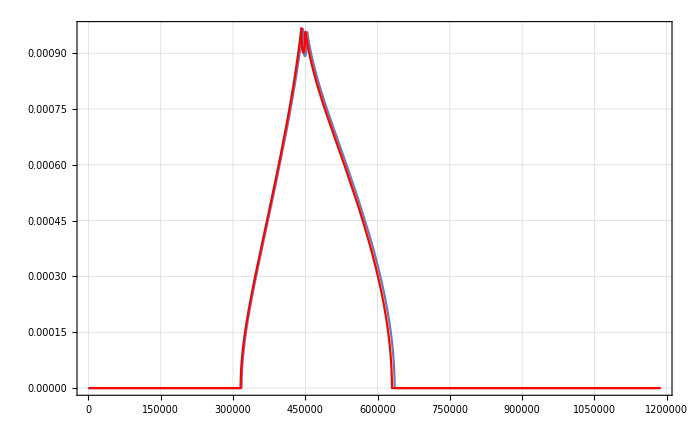

```mathematica
Show[
Plot[ManualphiAIntegrandAllLimitsShift[0.,0.,0.,{0.,0.,p,Pi/4},{Pi,0.2,1.,1.,1.,1.,1.,1.},{XAShift,YAShift,XDetShift,YDetShift},{0.06,0.05,0.9,0.,-0.9,0.1,0.09,0.9,0.,-0.9},{0.01,0.035,-0.03,0.}],{p,0,pmax}],
Plot[ManualphiAIntegrandAllLimitsShift[0.,0.,0.,{0.,0.,p,Pi/4},{Pi,0.2,1.,1.,1.,1.,1.,1.},{0.0,0.,0.,0.},{0.06,0.05,0.9,0.,-0.9,0.1,0.09,0.9,0.,-0.9},{0.01,0.035,-0.03,0.}],{p,0,pmax},PlotStyle->Red,PlotRange->All]
]
```

```mathematica
Step1IntShift[0.,0.,0.,{0.,Pi/4},{Pi,0.2,1.,1.,1.,1.,1.,1.},{XAShift,YAShift,XDetShift,YDetShift},{0.06,0.05,0.9,0.,-0.9,0.1,0.09,0.9,0.,-0.9},{0.01,0.035,-0.03,0.},{"GlobalAdaptive",Method->"MultidimensionalRule"},4,4,0,1]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 2 recursive bisections in p near {p,phiDV} = {628257.,2.16219}. NIntegrate obtained 1085.59 and 0.450995 for the integral and error estimates.

1085.59

```mathematica
Step1IntShift[0.,0.,0.,{0.,Pi/4},{Pi,0.2,1.,1.,1.,1.,1.,1.},{XAShift,YAShift,XDetShift,YDetShift},{0.06,0.05,0.9,0.,-0.9,0.1,0.09,0.9,0.,-0.9},{0.01,0.035,-0.03,0.},{"GlobalAdaptive",Method->"MultidimensionalRule"},4,4,0,2]
```

1085.57

```mathematica
Step1IntShift[0.,0.,0.,{0.,Pi/4},{Pi,0.2,1.,1.,1.,1.,1.,1.},{0.,0.,0.,0.},{0.06,0.05,0.9,0.,-0.9,0.1,0.09,0.9,0.,-0.9},{0.01,0.035,-0.03,0.},{"GlobalAdaptive",Method->"MultidimensionalRule"},4,4,0,2]
```

1070.56